## Selfing

## Model

We model the change in the distribution of the number i of mutations at a single locus in a population of diploids as a result of selection, mutation and reproduction by selfing.

### Parameters

#### Genotype frequencies

x0, x1, and x2 represent the frequencies of the genotypes with 0, 1, and 2 mutations, respectively.

```mathematica
x={x0,x1,x2}
```

{x0,x1,x2}

#### Fitness

s < 0 is the deleterious effect of a mutation in a homozygous state.

```mathematica
w={1,1+s/2,1+s}
```

{1,1+s/2,1+s}

#### Mean fitness

Equation S2 (Supplementary Information)

```mathematica
w̄=Total[x w]
```

x0+(1+s/2) x1+(1+s) x2

### Evolution

#### Effect of selection

```mathematica
Δsel=(x w)/(w̄)-x
```

{-x0+x0/(x0+(1+s/2) x1+(1+s) x2),-x1+((1+s/2) x1)/(x0+(1+s/2) x1+(1+s) x2),-x2+((1+s) x2)/(x0+(1+s/2) x1+(1+s) x2)}

#### Effect of mutation

μ is the deleterious mutation rate.  We assume that (i) an individual can, at most, acquire one mutation, and (ii) mutations are irreversible.

```mathematica
Δmut={-2 μ x0,2 μ x0- μ x1,μ x1}
```

{-2 x0 μ,2 x0 μ-x1 μ,x1 μ}

#### Effect of reproduction

```mathematica
Δself={x1/4,-x1/2,x1/4}
```

{x1/4,-x1/2,x1/4}

#### Combined effects of mutation, selection, and reproduction

Equation S17: genotype frequencies in the following generation

```mathematica
nextx=x+Δsel+Δmut+Δself//Simplify
```

{x1/4+x0 (1/(x0+x1+(s x1)/2+x2+s x2)-2 μ),-x1/2+((2+s) x1)/(2 x0+(2+s) x1+2 (1+s) x2)+2 x0 μ-x1 μ,x1/4+((1+s) x2)/(x0+x1+(s x1)/2+x2+s x2)+x1 μ}

```mathematica
Simplify[nextx=={ x0/(w̄)-2 μ x0+x1/4,((2+s) x1)/(2 w̄)+2 μ x0- μ x1-x1/2,((1+s) x2)/(w̄)+μ x1+x1/4}]
```

True

## Equilibrium

### Equilibrium

There are three equilibria, but only the second and third equilibria have x0 > 0

```mathematica
sol=Solve[nextx==x,{x0,x1,x2}]//FullSimplify
```

{{x0→0,x1→0,x2→1},{x0→((s (-1+s+2 (1+s) μ) (1+2 s+5 (1+s) μ+4 (1+s) μ^2)+√(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))) (√(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))+s (s+8 s μ (1+μ)+(1+μ) (1+2 μ) (1+4 μ)-s^2 (1+2 μ) (2+μ (5+4 μ)))))/(4 s^4 μ (1+μ) (3+4 μ)^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)),x1→1/(s^3 (1+μ) (3+4 μ)^2)(-2 s (1+μ) (1+2 μ) (1+4 μ)-2 √(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))-2 s^2 (1+8 μ (1+μ))+2 s^3 (1+2 μ) (2+μ (5+4 μ))),x2→-(((1+4 μ) (-2 (1+μ) √(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))+s^4 (1+2 μ)^2 (2+μ (5+4 μ))+s^2 (1+μ) (-3+2 μ (-3+6 μ+8 μ^2))-s (1+2 μ) (2 (1+μ)^2 (1+4 μ)+√(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))+s^3 (3+2 μ (15+2 μ (22+3 μ (9+4 μ))))))/(2 s^3 (1+μ) (3+4 μ)^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)))},{x0→((-s (-1+s+2 (1+s) μ) (1+2 s+5 (1+s) μ+4 (1+s) μ^2)+√(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))) (-s (1+μ) (1+2 μ) (1+4 μ)+√(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))-s^2 (1+8 μ (1+μ))+s^3 (1+2 μ) (2+μ (5+4 μ))))/(4 s^4 μ (1+μ) (3+4 μ)^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)),x1→1/(s^3 (1+μ) (3+4 μ)^2)2 (-s (1+μ) (1+2 μ) (1+4 μ)+√(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))-s^2 (1+8 μ (1+μ))+s^3 (1+2 μ) (2+μ (5+4 μ))),x2→-(((1+4 μ) (2 (1+μ) √(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))+s^4 (1+2 μ)^2 (2+μ (5+4 μ))+s^2 (1+μ) (-3+2 μ (-3+6 μ+8 μ^2))+s (1+2 μ) (-2 (1+μ)^2 (1+4 μ)+√(s^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)^2 ((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))+s^3 (3+2 μ (15+2 μ (22+3 μ (9+4 μ))))))/(2 s^3 (1+μ) (3+4 μ)^2 (1+2 s+5 (1+s) μ+4 (1+s) μ^2)))}}

The third equilibrium only produces valid genotype frequencies when mutations have large effects.

```mathematica
Reduce[{0≤Values[sol[[3]][[1]]]≤1,0≤Values[sol[[3]][[2]]]≤1,0≤Values[sol[[3]][[3]]]≤1,0<μ<1,-1≤s<0}]
```

0<μ<1&&(-1≤s<(-1-5 μ-4 μ^2)/(2+5 μ+4 μ^2)||s==-1/2 √((1+4 μ)/((2+5 μ+4 μ^2)^2))+(-1-6 μ-8 μ^2)/(2 (2+5 μ+4 μ^2)))

Equation S18

```mathematica
Reduce[{1+2 s+5 (1+s) μ+4 (1+s) μ^2>0,0<μ<1,-1≤s<0}]
```

0<μ<1&&(-1-5 μ-4 μ^2)/(2+5 μ+4 μ^2)<s<0

```mathematica
eq=FullSimplify[sol[[2]],Assumptions->{0<μ<1,(-1-5 μ-4 μ^2)/(2+5 μ+4 μ^2)≤s<0}]
```

{x0→1/(4 s^2 μ (1+μ) (3+4 μ)^2)(-1+s+2 μ+2 s μ-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)) (1+s-2 s^2+7 μ+8 s μ-9 s^2 μ+14 μ^2+8 s μ^2-14 s^2 μ^2+8 μ^3-8 s^2 μ^3-(1+2 s+5 (1+s) μ+4 (1+s) μ^2) √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)),x1→1/(s^2 (1+μ) (3+4 μ)^2)2 (-(1+μ) (1+2 μ) (1+4 μ)+(1+2 s+5 (1+s) μ+4 (1+s) μ^2) √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)-s (1+8 μ (1+μ))+s^2 (1+2 μ) (2+μ (5+4 μ))),x2→-1/(2 s^2 (1+μ) (3+4 μ)^2)(1+4 μ) ((s+2 s μ)^2+2 (1+μ) (-1-2 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))+s (1+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (4+4 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))))}

```mathematica
γ=√((1-s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2);ϵ=1/(s^2 (1+μ) (3+4 μ)^2);
```

```mathematica
Simplify[Values[eq]=={ϵ/2(2+5 s+11 s^2+2μ (7+s (22+19 s)) +4 μ^2 (1+s) (7+11 s)+16 μ^3 (1+s)^2 -γ(2+7 s+2 (5+7 s) μ+8 μ^2(1+s) ) ),2ϵ (s (-1+2γ+μ(-8 + 5γ+4μ(-2+γ )))+s^2 (1+2 μ) (2+μ (5+4 μ))+ (1+μ) (1+4 μ)(-1+γ-2 μ)),-ϵ/2(1+4 μ) ((s+2 s μ)^2+2 (1+μ) (-1+γ-2 μ)+s (1+γ+2 μ (4+γ+4 μ)))}]
```

True

### Stability

#### Jacobian matrix

```mathematica
f=nextx/.{x2->1-x0-x1}//FullSimplify
```

{x1/4-(2 x0)/(-2+s (-2+2 x0+x1))-2 x0 μ,-x1/2-((2+s) x1)/(-2+s (-2+2 x0+x1))+2 x0 μ-x1 μ,x1/4+(2 (1+s) (-1+x0+x1))/(-2+s (-2+2 x0+x1))+x1 μ}

Equation S19

```mathematica
j=({{D[f[[1]],x0], D[f[[1]],x1]}, {D[f[[2]],x0], D[f[[2]],x1]}})//Simplify
```

{{(4 s x0)/(-2+s (-2+2 x0+x1))^2-2/(-2+s (-2+2 x0+x1))-2 μ,1/4+(2 s x0)/(-2+s (-2+2 x0+x1))^2},{2 ((s (2+s) x1)/(-2+s (-2+2 x0+x1))^2+μ),-1/2+(s (2+s) x1)/(-2+s (-2+2 x0+x1))^2-(2+s)/(-2+s (-2+2 x0+x1))-μ}}

```mathematica
Simplify[j=={{1/(w̄)+(s x0)/(w̄)^2-2 μ,1/4+(s x0)/(2(w̄)^2)},{(s (2+s) x1)/(2(w̄)^2)+2μ,-1/2+(2+s)/(2 w̄)+(s (2+s) x1)/(4(w̄)^2)-μ}}/.{x2->1-x0-x1}]
```

True

#### Jacobian matrix evaluated at equilibrium

```mathematica
jeq=j/.eq//FullSimplify
```

{{1/(2 s (2+s))(s^3 (1+2 μ)^2-(1+4 μ) (-1-2 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))+s (7-4 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (7+10 μ-3 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))+s^2 (3-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (6+8 μ-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))),1/(4 s (2+s))(s^3 (1+2 μ)^2-s^2 (1+2 μ) (-3-8 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))-(1+4 μ) (-1-2 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))+s (4-3 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (8+10 μ-3 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))))},{1/(s (2+s))(-s^3 μ (1+2 μ)+(1+4 μ) (-1-2 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))+s^2 (2+μ (-8 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))+s (-1+2 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+μ (-5-14 μ+5 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))),1/(4 s (2+s))(s^3 (1-4 μ^2)+2 (1+4 μ) (-1-2 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))+s^2 (9-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (1-8 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))+2 s (2+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+μ (-7-14 μ+5 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))))}}

#### Characteristic equation of the Jacobian matrix

Equation S12

```mathematica
a=CoefficientList[CharacteristicPolynomial[jeq,y],y]//FullSimplify
```

{1/(4 (2+s)^2)(23+s^4 (1+2 μ)^3-15 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)-s^3 (1+2 μ)^2 (-6-12 μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))+2 μ (23-12 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (15+6 μ-5 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))+s (31-22 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (47-23 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (36+20 μ-9 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))))+s^2 (11-7 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (35-11 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (36+24 μ-5 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))))),1/4 (-s (3+4 μ (2+μ))+3 (-3+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))-1/(2+s)2 μ (7+6 μ-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+s (5+4 μ-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))),1}

```mathematica
Simplify[a=={1/(4 (2+s)^2)(23-15 γ+2 μ (23-12 γ+2 μ (15-5 γ+6 μ))+s (31-22 γ+2 μ (47-23 γ+2 μ (36-9 γ+20 μ)))+s^2 (11-7 γ+2 μ (35-11 γ+2 μ (36-5 γ+24 μ)))+s^3 (1+2 μ)^2 (6-γ+12 μ)+s^4 (1+2 μ)^3),-1/4 (9-3γ+s (3+4 μ (2+μ))+(2 μ)/(2+s) (7-γ+6 μ+s (5-γ+4 μ))),1}]
```

True

```mathematica
pol[λ_]:=a[[1]]+a[[2]]λ+λ^2
```

```mathematica
b=CoefficientList[pol[y+1],y]//FullSimplify
```

{1/(4 (2+s)^2)(3+s^4 (1+2 μ)^3-3 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (9-10 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (9+6 μ-5 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))+s^3 (1+2 μ) (3-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+2 μ (11+12 μ-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))+s (-1-10 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+4 μ (7-10 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+μ (25+20 μ-9 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))))-2 s^2 (3+2 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)-2 μ (7-5 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+μ (30+24 μ-5 √((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))))),1/4 (8-s (3+4 μ (2+μ))+3 (-3+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))-1/(2+s)2 μ (7+6 μ-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)+s (5+4 μ-√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2)))),1}

```mathematica
Simplify[b=={1+a[[1]]+a[[2]],2+a[[2]],1}]
```

True

#### Stability condition

Equations S13 and S20: Routh-Hurwitz conditions for stability

```mathematica
stab=Reduce[{b[[1]]>0,b[[2]]>0,0<μ<1,-1≤s<0}]
```

(-1≤s≤1/22 (-15+√5)&&0<μ<1)||(1/22 (-15+√5)<s<0&&0<μ<1/8 √((1-7 s)/(1+s))+(-1-5 s)/(8 (1+s)))

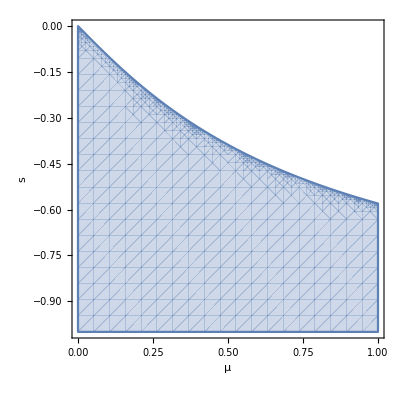

```mathematica
RegionPlot[stab,{μ,0,1},{s,-1,0},FrameLabel->Automatic,LabelStyle->Medium,MaxRecursion->5]
```

The equilibrium is also valid if the stability condition is met.

```mathematica
valid=Reduce[{0≤Values[eq[[1]]]≤1,0≤Values[eq[[2]]]≤1,0≤Values[eq[[3]]]≤1,0<μ<1,-1≤s<0}]
```

(-1≤s≤1/22 (-15+√5)&&0<μ<1)||(1/22 (-15+√5)<s<0&&0<μ≤1/8 √((1-7 s)/(1+s))+(-1-5 s)/(8 (1+s)))

### Mean fitness at equilibrium (1 locus)

Equation S21

```mathematica
ŵ=w̄/.eq//FullSimplify
```

(5+s+6 μ+2 s μ+√((-1+s)^2+4 (1+s+s^2) μ+4 (1+s)^2 μ^2))/(2 (1+μ) (3+4 μ))

```mathematica
Simplify[ŵ==(5+s+6 μ+2 s μ+γ)/(2 (1+μ) (3+4 μ))]
```

True

### Mean fitness at equilibrium (L loci)

If there are L fitness loci with the same μ and s, and there is linkage equilibrium between the loci, the mean fitness at equilibrium will be (ŵ)^L.  Taking a first-order Taylor expansion of ln((ŵ)^L) we get

```mathematica
FullSimplify[Series[Log[(ŵ)^L],{μ,0,1}],Assumptions->1-s>0]
```

Series::ztest1: Unable to decide whether numeric quantity Indeterminate is equal to zero. Assuming it is.

((L-2 L s) μ)/(-1+s)+O[μ]^2

Equation S22

```mathematica
Solve[Log[y]==((L-2 L s) μ)/(-1+s),{y}]
```

{{y→ConditionalExpression[ⅇ^(-((-L+2 L s) μ)/(-1+s)),-π≤Im[((-L+2 L s) μ)/(-1+s)]<π]}}

U is the deleterious mutation rate per diploid genome per generation.

```mathematica
U=2L μ
```

2 L μ

```mathematica
Simplify[ⅇ^(-((-L+2 L s) μ)/(-1+s))==ⅇ^(-U((1-2 s)/(2-2 s)))]
```

True

## Compared to amitosis

```mathematica
Manipulate[Plot[{ⅇ^(-U((1-2 s)/(2-2 s))),ⅇ^(-U((1-3 s)/(2-3 s))),ⅇ^-U},{U,10^-5,1},AxesLabel->{U,Ŵ},PlotLegends->{"Selfing","Amitosis", "Mitosis"}],{{s,-.1,"s"},-1,0,Appearance->"Labeled"}]
```